```mathematica
Clear["Global`*"]
```

```mathematica
P=({{0.25, 0.5, 0.25}, {0, 0.5, 0.5}, {1/3, 1/3, 1/3}});
q={0,0.5,0.5}
mc=DiscreteMarkovProcess[q,P]
Graph[mc,VertexLabels->{1-> "Не читает",2-> "Част. читает",3->"Все читает"}]
```

{0,0.5,0.5}

DiscreteMarkovProcess[{0,0.5,0.5},{{0.25,0.5,0.25},{0,0.5,0.5},{1/3,1/3,1/3}}]

Цепь Маркова неразложима, если можно достичь любого состояния из любого другого состояния (необязательно, что за один шаг времени). Если пространство состояний конечно и цепь можно представить в виде графа, то мы можем сказать, что граф неразложимой цепи Маркова сильно связный (теория графов).

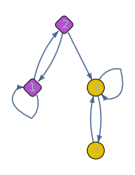

DiscreteMarkovProcess[1,{{0.3,0.7,0,0},{0.4,0,0.6,0},{0,0,0.5,0.5},{0,0,1,0}}]

CommunicatingClasses (неразложимая цепь) | {{3,4},{1,2}}
RecurrentClasses (возвратная цепь) | {{3,4}}
TransientClasses (невозвратная цепь) | {{1,2}}
AbsorbingClasses (поглощающее состояние) | {}
PeriodicClasses (периодическая/циклическая цепь) | {}
Periods (переодическая) | {}
Irreducible (неприводимая/неразложимая) | False
Aperiodic (непереодическая) | True
Primitive (простая цепью) | False

```mathematica
P={{0.3,0.7,0,0},{0.4,0,0.6,0},{0,0,0.5,0.5},{0,0,1,0}};
mc1=DiscreteMarkovProcess[1,P];
Graph[mc1]
proc=mc1
Grid[{
{"CommunicatingClasses (неразложимая цепь)",MarkovProcessProperties[proc,"CommunicatingClasses"]},
{"RecurrentClasses (возвратная цепь)",MarkovProcessProperties[proc,"RecurrentClasses"]},
{"TransientClasses (невозвратная цепь)",MarkovProcessProperties[proc,"TransientClasses"]},
{"AbsorbingClasses (поглощающее состояние)",MarkovProcessProperties[proc,"AbsorbingClasses"]},
{"PeriodicClasses (периодическая/циклическая цепь)",MarkovProcessProperties[proc,"PeriodicClasses"]},
{"Periods (переодическая)",MarkovProcessProperties[proc,"Periods"]},
{"Irreducible (неприводимая/неразложимая)",MarkovProcessProperties[proc,"Irreducible"]},
{"Aperiodic (непереодическая)",MarkovProcessProperties[proc,"Aperiodic"]},
{"Primitive (простая цепью)",MarkovProcessProperties[proc,"Primitive"]}
}]
```

Состояние имеет период k, если при уходе из него для любого возврата в это состояние нужно количество этапов времени, кратное k (k — наибольший общий делитель всех возможных длин путей возврата). Если k = 1, то говорят, что состояние является апериодическим, а вся цепь Маркова является апериодической, если апериодичны все её состояния. В случае неприводимой цепи Маркова можно также упомянуть, что если одно состояние апериодическое, то и все другие тоже являются апериодическими.

{{0,1,0,0},{0.4,0,0.6,0},{0,0.5,0,0.5},{0,0,1,0}}

{{0,0.5,0,0.5,0},{0,0,1,0,0},{1,0,0,0,0},{0,0,0,0,1},{1,0,0,0,0}}

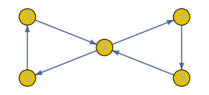

DiscreteMarkovProcess[1,{{0,0.5,0,0.5,0},{0,0,1,0,0},{1,0,0,0,0},{0,0,0,0,1},{1,0,0,0,0}}]

CommunicatingClasses (неразложимая цепь) | {{1,2,3,4,5}}
RecurrentClasses (возвратная цепь) | {{1,2,3,4,5}}
TransientClasses (невозвратная цепь) | {}
AbsorbingClasses (поглощающее состояние) | {}
PeriodicClasses (периодическая/циклическая цепь) | {{1,2,3,4,5}}
Periods (переодическая) | {3}
Irreducible (неприводимая/неразложимая) | True
Aperiodic (непереодическая) | False
Primitive (простая цепью) | False

```mathematica
P1={{0,1,0,0},{0.4,0,0.6,0},{0,0.5,0,0.5},{0,0,1,0}}
P2={{0,0.5,0,0.5,0},{0,0,1,0,0},{1,0,0,0,0},{0,0,0,0,1},{1,0,0,0,0}}
mc2=DiscreteMarkovProcess[1,P2];
Graph[mc2]
proc=mc2
Grid[{
{"CommunicatingClasses (неразложимая цепь)",MarkovProcessProperties[proc,"CommunicatingClasses"]},
{"RecurrentClasses (возвратная цепь)",MarkovProcessProperties[proc,"RecurrentClasses"]},
{"TransientClasses (невозвратная цепь)",MarkovProcessProperties[proc,"TransientClasses"]},
{"AbsorbingClasses (поглощающее состояние)",MarkovProcessProperties[proc,"AbsorbingClasses"]},
{"PeriodicClasses (периодическая/циклическая цепь)",MarkovProcessProperties[proc,"PeriodicClasses"]},
{"Periods (переодическая)",MarkovProcessProperties[proc,"Periods"]},
{"Irreducible (неприводимая/неразложимая)",MarkovProcessProperties[proc,"Irreducible"]},
{"Aperiodic (непереодическая)",MarkovProcessProperties[proc,"Aperiodic"]},
{"Primitive (простая цепью)",MarkovProcessProperties[proc,"Primitive"]}
}]
```

Состояние является невозвратным, если при уходе из состояния существует ненулевая вероятность того, что мы никогда в него не вернёмся. И наоборот, состояние считается возвратным, если мы знаем, что после ухода из состояния можем в будущем вернуться в него с вероятностью 1 (если оно не является невозвратным).

```mathematica
-Graphics-
P3={{,,,,},{,,,,},{,,,,},{,,,,},{,,,,}}
P4={{,,,,},{,,,,},{,,,,},{,,,,},{,,,,}}
mc3=DiscreteMarkovProcess[1,P3];
Graph[mc3]
proc=mc3
Grid[{
{"CommunicatingClasses (неразложимая цепь)",MarkovProcessProperties[proc,"CommunicatingClasses"]},
{"RecurrentClasses (возвратная цепь)",MarkovProcessProperties[proc,"RecurrentClasses"]},
{"TransientClasses (невозвратная цепь)",MarkovProcessProperties[proc,"TransientClasses"]},
{"AbsorbingClasses (поглощающее состояние)",MarkovProcessProperties[proc,"AbsorbingClasses"]},
{"PeriodicClasses (периодическая/циклическая цепь)",MarkovProcessProperties[proc,"PeriodicClasses"]},
{"Periods (переодическая)",MarkovProcessProperties[proc,"Periods"]},
{"Irreducible (неприводимая/неразложимая)",MarkovProcessProperties[proc,"Irreducible"]},
{"Aperiodic (непереодическая)",MarkovProcessProperties[proc,"Aperiodic"]},
{"Primitive (простая цепью)",MarkovProcessProperties[proc,"Primitive"]}
}]
```

## Конечные цепи Маркова: задача о рынке труда

### Задача от занятости на рынке труда Рассмотрим человека, который в любой момент времени t, находится в одном из двух состояний: “работает” (состояние 1) или “без работы” ( состояние 2) работник переходит из состояния “работает” в состояние “без работы” с вероятностью α работник переходит из состояния “без работы” в состояние “работает” с вероятностью β

Зададим матрицу вероятностей перехода

```mathematica
Clear["Global`*"]
P=({{1-α, α}, {β, 1-β}})
α=0.2 (*вероятность потерять работу*)
β=0.6 (*вероятность найти работу*)
P//MatrixForm
```

{{1-α,α},{β,1-β}}

0.2

0.6

(0.8 | 0.2
0.6 | 0.4)

Найдем цепь конечную цепь маркова с дискретным временем и исходным состоянием 1 и 
найдем вероятность нахождения в состоянии 1 (работает) и 2 (безработный)
 [Способ 1, аналитически]

```mathematica
dp=DiscreteMarkovProcess[2,P];

PDF[StationaryDistribution[dp],1]
PDF[StationaryDistribution[dp],2]
```

0.75

0.25

Найдем цепь конечную цепь маркова с дискретным временем и исходным состоянием 2 и 
найдем вероятность нахождения в состоянии 1 (работает) и 2 (безработный)  
[Способ 2, аналитически]

```mathematica
dp=DiscreteMarkovProcess[1,P];

Probability[n==1,n\[Distributed]StationaryDistribution[dp]]
Probability[n==2,n\[Distributed]StationaryDistribution[dp]]

StationaryDistribution[dp]
```

0.75

0.25

ProbabilityDistribution[0.75 Boole[x==1]+0.25 Boole[x==2],{x,1,2,1}]

Найдем цепь конечную цепь маркова с дискретным временем и исходным состоянием 1 и 
найдем вероятность нахождения в состоянии 1 (работает) и 2 (безработный)  
[Способ 3, численно]

```mathematica
dp=DiscreteMarkovProcess[1,P];

NProbability[n==1,n\[Distributed]StationaryDistribution[dp]]
NProbability[n==2,n\[Distributed]StationaryDistribution[dp]]
```

0.75

0.25

Найти стационарное (эргодическое) распределение цепи Маркова (это такое распределение вероятности, которое не меняется с течением времени):

```mathematica
dist=StationaryDistribution[dp]
```

ProbabilityDistribution[0.75 Boole[x==1]+0.25 Boole[x==2],{x,1,2,1}]

Найти стационарное (эргодическое) распределение цепи Маркова (это такое распределение вероятности, которое не меняется с течением времени):

```mathematica
dist=StationaryDistribution[dp]
```

ProbabilityDistribution[0.75 Boole[x==1]+0.25 Boole[x==2],{x,1,2,1}]

Вероятность состояния на каждом шаге

```mathematica
dp1=DiscreteMarkovProcess[1,P]; (*исходное состоянием 1*)
 (*1 шаг*) PDF[dp1[1],t]  
 (*2 шаг*) PDF[dp1[2],t]  
(*3 шаг*)  PDF[dp1[3],t]   
(*5 шаг*)  PDF[dp1[5],t]
(*12 шаг*) PDF[dp1[12],t]
```

0.8 Boole[1==t]+0.2 Boole[2==t]

0.76 Boole[1==t]+0.24 Boole[2==t]

0.752 Boole[1==t]+0.248 Boole[2==t]

0.75008 Boole[1==t]+0.24992 Boole[2==t]

0.75 Boole[1==t]+0.25 Boole[2==t]

```mathematica
dp2=DiscreteMarkovProcess[2,P]; (*исходное состоянием 2*)
 (*1 шаг*) PDF[dp2[1],t]  
 (*2 шаг*) PDF[dp2[2],t]  
(*3 шаг*)  PDF[dp2[3],t]   
(*5 шаг*)  PDF[dp2[5],t]
(*12 шаг*)PDF[dp2[12],t]
```

0.6 Boole[1==t]+0.4 Boole[2==t]

0.72 Boole[1==t]+0.28 Boole[2==t]

0.744 Boole[1==t]+0.256 Boole[2==t]

0.74976 Boole[1==t]+0.25024 Boole[2==t]

0.75 Boole[1==t]+0.25 Boole[2==t]

Вероятность состояния на каждом шаге, исходное состояние 1, вероятность в первом состоянии

0.75

0.8

0.76

0.752

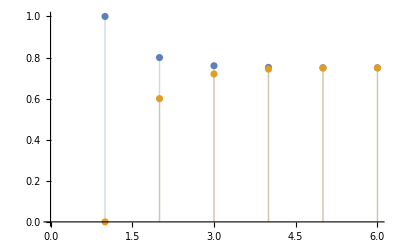

```mathematica
PDF[dp1[∞],1]
PDF[dp1[1],1]
PDF[dp1[2],1]
PDF[dp1[3],1]
ListPlot[{
Table[PDF[dp1[t],1],{t,0,5}],
Table[PDF[dp2[t],1],{t,0,5}]
},PlotRange->{0,1},Filling->Axis]
```

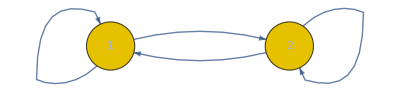

```mathematica
Graph[dp1]
```

#### First Passage Time - время первого достижения First Passage Time Distribution - распределение времени вхождения в заданное состояние

Какова вероятность проработать в течении трех/десяти месяцев, если сначала была работа?

```mathematica
Probability[t[1]==1&&t[2]==1&&t[3]==1,t\[Distributed]dp1](*исходное состояние задавать не нужно, берется из процесса*)
1-CDF[FirstPassageTimeDistribution[dp1,2],3]//N (*1 - накопленная вероятность распределения вероятности вхождения в первый раз в состояние 2 в течении 3 циклов*)
Likelihood[dp1,{1,1,1,1}](*исходное состояние обязательно нужно, определяется вероятность получения заданной последовательности *)
```

0.512

0.512

0.512

```mathematica
1-CDF[FirstPassageTimeDistribution[dp1,2],10]//N
Likelihood[dp1,Array[1&,11]]
```

0.107374

0.107374

Какова вероятность проработать в течении трех/десяти месяцев, если сначала  работы не было?

```mathematica
Probability[t[1]==1&&t[2]==1&&t[3]==1,t\[Distributed]dp2](*исходное состояние задавать не нужно, берется из процесса*)
Likelihood[dp2,{2,1,1,1}](*исходное состояние обязательно нужно, определяется вероятность получения заданной последовательности *)
1-CDF[FirstPassageTimeDistribution[dp2,2],3]//N (*1 - накопленная вероятность распределения вероятности вхождения в первый раз в состояние 2 в течении 3 циклов*)
```

0.384

0.384

0.384

```mathematica
1-CDF[FirstPassageTimeDistribution[dp2,2],10]//N
Likelihood[dp2,Prepend[Array[1&,10],2] ]
```

0.0805306

0.0805306

Какова вероятность потерять работу хотя бы один раз в течении 10 мес, если сначала была работа?

```mathematica
CDF[FirstPassageTimeDistribution[dp1,2],10]//N
1-Likelihood[dp1,Array[1&,11]]
```

0.892626

0.892626

Какова вероятность потерять работу только один раз в течении 10 мес, если сначала была работа?

```mathematica
Permutations[Prepend[Array[1&,10],2] ]
%[[2;;All]]
(Likelihood[dp1,#]&/@Permutations[Prepend[Array[1&,10],2] ][[2;;All]])
Plus@@(Likelihood[dp1,#]&/@Permutations[Prepend[Array[1&,10],2] ][[2;;All]])
```

{{2,1,1,1,1,1,1,1,1,1,1},{1,2,1,1,1,1,1,1,1,1,1},{1,1,2,1,1,1,1,1,1,1,1},{1,1,1,2,1,1,1,1,1,1,1},{1,1,1,1,2,1,1,1,1,1,1},{1,1,1,1,1,2,1,1,1,1,1},{1,1,1,1,1,1,2,1,1,1,1},{1,1,1,1,1,1,1,2,1,1,1},{1,1,1,1,1,1,1,1,2,1,1},{1,1,1,1,1,1,1,1,1,2,1},{1,1,1,1,1,1,1,1,1,1,2}}

{{1,2,1,1,1,1,1,1,1,1,1},{1,1,2,1,1,1,1,1,1,1,1},{1,1,1,2,1,1,1,1,1,1,1},{1,1,1,1,2,1,1,1,1,1,1},{1,1,1,1,1,2,1,1,1,1,1},{1,1,1,1,1,1,2,1,1,1,1},{1,1,1,1,1,1,1,2,1,1,1},{1,1,1,1,1,1,1,1,2,1,1},{1,1,1,1,1,1,1,1,1,2,1},{1,1,1,1,1,1,1,1,1,1,2}}

{0.0201327,0.0201327,0.0201327,0.0201327,0.0201327,0.0201327,0.0201327,0.0201327,0.0201327,0.0268435}

0.208037

Сколько в среднем нужно потратить времени на поиск работы (естественно, исходное состояние работы нет) ?
(First Passage Time Distribution - распределение времени вхождения в заданное состояние)

```mathematica
Mean[FirstPassageTimeDistribution[dp2,1]]//N
```

1.66667

Сколько в среднем работник проработает на одном месте (естественно, исходное состояние работа есть) ?

```mathematica
Mean[FirstPassageTimeDistribution[dp1,2]]//N
```

5.

Средняя время занятости в состоянии работы/безработицы

```mathematica
MarkovProcessProperties[dp1,"HoldingTimeMean"](*среднее время занятости *)
```

{4.,0.666667}

Имитация состояния человека на период 12 периодов 
(исходное состояние 1)

TemporalData[…]

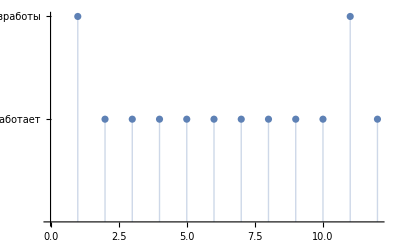

```mathematica
dp11=DiscreteMarkovProcess[1,P];
rf=RandomFunction[dp11,{1,12}]
ListPlot[rf,Ticks->{Automatic,{{1,"Работает"},{2,"Безработы"}}},Filling->Axis]
```

Имитация состояния человека на период 12 периодов 
(исходное состояние 2)

TemporalData[…]

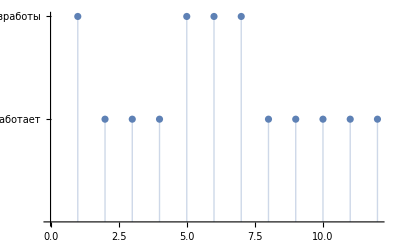

```mathematica
dp22=DiscreteMarkovProcess[2,P];
rf=RandomFunction[dp22,{1,12}]
ListPlot[rf,Ticks->{Automatic,{{1,"Работает"},{2,"Безработы"}}},Filling->Axis]
```

Имитационное моделирование по нахождению состояния занятости человек на выборке k

```mathematica
k=100000;
rf=RandomFunction[dp,{1,k}]["Values"];
Count[rf,1]/k  //N
Count[rf,2]/k   //N
```

0.74833

0.25167

## Модель погоды

### Предполагается, что мы один раз в день (например, в полдень) смотрим в окно и регистрируем в журнале текущее состояние погоды. Мы условились, что лишь одно из трех ниже названных состояний в день мы записываем в журнал: Состояние № 1: дождь (или снег) Состояние № 2: пасмурно Состояние № 3: ясно:

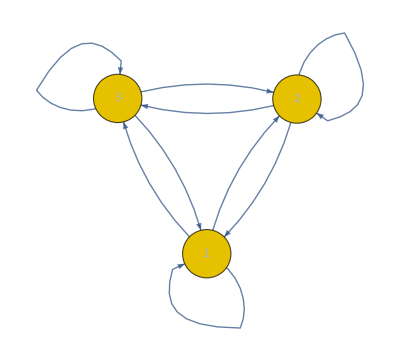

```mathematica
Pg={{0.4,0.3,0.3},{0.2,0.6,0.2},{0.1,0.1,0.8}};
proc=DiscreteMarkovProcess[3,Pg];
Graph[proc]
```

Исходя из того, что погода в первый день (t =1) ясная (состояние 3), мы можем задать себе вопрос: какова вероятность (согласно нашей модели), что следующие 7 дней будет именно «ясно — ясно — дождь — дождь — ясно — пасмурно — ясно»?

```mathematica
1*Pg[[3,3]]Pg[[3,3]]Pg[[3,1]]Pg[[1,1]]Pg[[1,3]]Pg[[3,2]]Pg[[2,3]]
Likelihood[proc,{3,3,3,1,1,3,2,3}]
```

0.0001536

0.0001536

Вычислим среднее время, в течение которого система сохранит свое состояние

```mathematica
1/(1-Pg[[1,1]])
1/(1-Pg[[2,2]])
1/(1-Pg[[3,3]])
MarkovProcessProperties[proc,"HoldingTimeMean"]
```

1.66667

2.5

5.

{0.666667,1.5,4.}

```mathematica
proc=DiscreteMarkovProcess[3,Pg];
Mean[FirstPassageTimeDistribution[proc,1] ]
Mean[FirstPassageTimeDistribution[proc,2] ]
Mean[FirstPassageTimeDistribution[proc,3] ]
MarkovProcessProperties[proc,"HoldingTimeMean"]
```

8.33333

7.77778

1.83333

{0.666667,1.5,4.}

```mathematica
StationaryDistribution[proc]
PDF[proc[100],1]
PDF[proc[0],1]
```

ProbabilityDistribution[0.181818 Boole[x==1]+0.272727 Boole[x==2]+0.545455 Boole[x==3],{x,1,3,1}]

0.181818

0

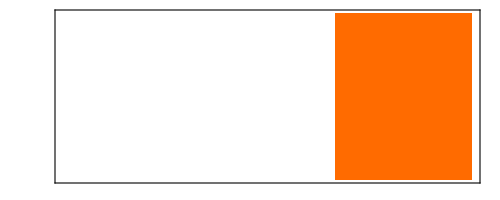
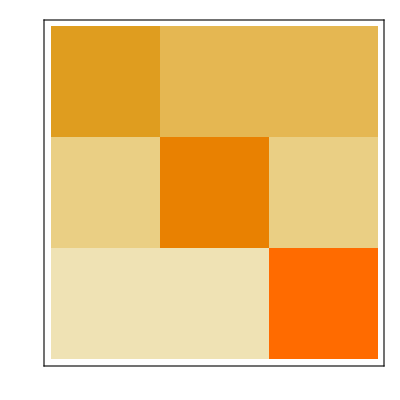
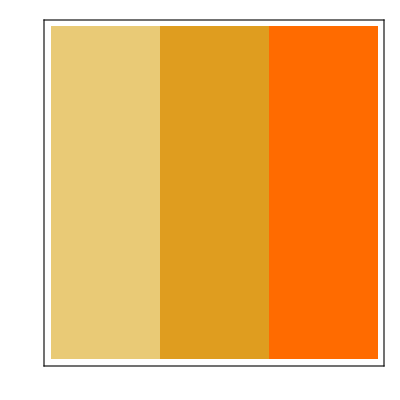
Basic Properties | 
InitialProbabilities | -Graphics-
TransitionMatrix | -Graphics-
HoldingTimeMean | {0.666667,1.5,4.}
HoldingTimeVariance | {1.11111,3.75,20.}
Structural Properties | 
CommunicatingClasses | {1,2,3}
RecurrentClasses | {1,2,3}
TransientClasses | None
AbsorbingClasses | None
PeriodicClasses | None
Periods | {}
Irreducible | True
Primitive | True
Aperiodic | True
Limiting Properties | 
LimitTransitionMatrix | -Graphics-
Reversible | True

```mathematica
MarkovProcessProperties[proc]
```

```mathematica
Pg={{0.4,0.3,0.3},{0.2,0.6,0.2},{0.1,0.1,0.8}};
Pg//MatrixForm
MatrixPower [Pg,2]//MatrixForm
MatrixPower [Pg,3]//MatrixForm
MatrixPower [Pg,4]//MatrixForm
MatrixPower [Pg,5]//MatrixForm
MatrixPower [Pg,6]//MatrixForm
MatrixPower [Pg,100]//MatrixForm
```

(0.4 | 0.3 | 0.3
0.2 | 0.6 | 0.2
0.1 | 0.1 | 0.8)

(0.25 | 0.33 | 0.42
0.22 | 0.44 | 0.34
0.14 | 0.17 | 0.69)

(0.208 | 0.315 | 0.477
0.21 | 0.364 | 0.426
0.159 | 0.213 | 0.628)

(0.1939 | 0.2991 | 0.507
0.1994 | 0.324 | 0.4766
0.169 | 0.2383 | 0.5927)

(0.18808 | 0.28833 | 0.52359
0.19222 | 0.30188 | 0.5059
0.17453 | 0.25295 | 0.57252)

(0.185257 | 0.281781 | 0.532962
0.187854 | 0.289384 | 0.522762
0.177654 | 0.261381 | 0.560965)

(0.181818 | 0.272727 | 0.545455
0.181818 | 0.272727 | 0.545455
0.181818 | 0.272727 | 0.545455)